# Fourier Transformation. Starter Code.

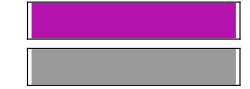

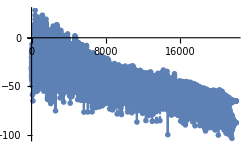

```mathematica
ClearAll["Global`*"]
record1 = Sound[SoundNote["G",1,"Violin"]]
Periodogram[record1]
```

#### Shifting sound by a fixed frequency

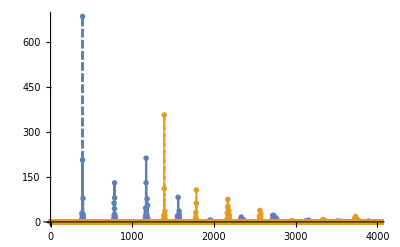

```mathematica
res=AudioFrequencyShift[record1,Quantity[1000,"Hertz"]]

Periodogram[{record1,res},PlotRange->{{0,4000},All},ScalingFunctions->"Absolute"]
```

#### Shifting sound using a given coefficient

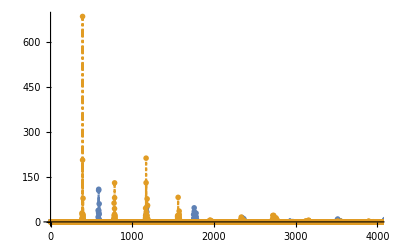

```mathematica
new = AudioPitchShift[record1, 1.5]
Periodogram[{new, record1},PlotRange->{{0,4000},All},ScalingFunctions->"Absolute"]
```

#### Working with data

```mathematica
(* get Amplitude data in time domain *)
AudioData[new]
AudioData[new][[1]];
AudioData[new][[2]];
ListPlot[AudioData[new][[1]]];
ListPlot[AudioData[new][[2]]];
```

{{1.00987×10^-8,6.48649×10^-8,1.72839×10^-7,6.97719×10^-7,1.1602×10^-6,-7.36842×10^-7,-7.37031×10^-6,-0.0000168434,-0.0000248575,-0.0000275612,-0.0000268305,45547,0.0354259,0.0278062,0.023525,0.0199708,0.016173,0.0161686,0.0179116,0.020459,0.0192367,0.012088},{1}}
 |  |  |  |

{{2.89219×10^-9,0.0000370022,0.000237798,0.000433334,0.000134153,0.000097621,0.00010709,0.000049158,0.000230403,0.000475326,45548,0.000208603,0.000475326,0.000230403,0.000049158,0.00010709,0.000097621,0.000134153,0.000433334,0.000237798,0.0000370022},{1}}
 |  |  |  |

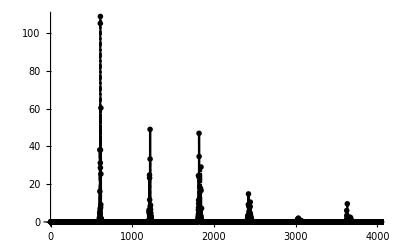

```mathematica
(* squared magnitude of the discrete Fourier transform (power spectrum) of list. *)
PerData = PeriodogramArray[new]
ListLinePlot[PerData,PlotRange->{{0, 4000}, All}]
```

{{63,0.0442331},{609,31.247},{1218,49.0094},{1817,46.9268},{2422,14.8239},{3025,0.759405},{3631,0.706855},{4288,1.50275},{4851,0.24716},{5452,0.316521},{6049,0.772099},{6692,0.00598606},{7258,0.534074},{7845,0.0690222},{8555,0.00917182},{9209,0.0437086},{9686,0.0101934},{10425,0.00253317},{10431,0.00248332},{11046,0.00189459},{11048,0.00191858},{11555,0.0017778},{11558,0.00155094},{11564,0.00310515},{12092,0.00179782},{12694,0.0010163},{13282,0.0003056},{13963,0.000116894},{13965,0.0000952705},{14737,0.000159083},{15122,0.000103559},{15723,0.000167165},{16570,0.000239331},{16906,0.0000965687},{17509,0.0000252091},{18212,0.0000195426},{18743,0.0000114083},{18745,0.0000124625},{19385,4.46353×10^-6},{19952,5.41181×10^-6},{20364,0.0000151164},{20969,0.0000390797},{21990,0.0000157588},{23580,0.0000157588},{24601,0.0000390797},{25206,0.0000151164},{25618,5.41181×10^-6},{26185,4.46353×10^-6},{26825,0.0000124625},{26827,0.0000114083},{27358,0.0000195426},{28061,0.0000252091},{28664,0.0000965687},{29000,0.000239331},{29847,0.000167165},{30448,0.000103559},{30833,0.000159083},{31605,0.0000952705},{31607,0.000116894},{32288,0.0003056},{32876,0.0010163},{33478,0.00179782},{34006,0.00310515},{34012,0.00155094},{34015,0.0017778},{34522,0.00191858},{34524,0.00189459},{35139,0.00248332},{35145,0.00253317},{35884,0.0101934},{36361,0.0437086},{37015,0.00917182},{37725,0.0690222},{38312,0.534074},{38878,0.00598606},{39521,0.772099},{40118,0.316521},{40719,0.24716},{41282,1.50275},{41939,0.706855},{42545,0.759405},{43148,14.8239},{43753,46.9268},{44352,49.0094},{44961,31.247},{45507,0.0442331}}

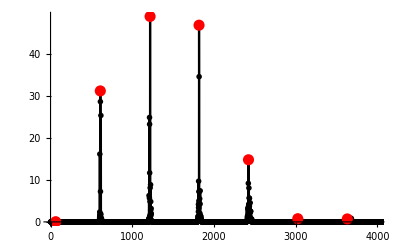

```mathematica
(*automatically find and plot peaks*)
peaks=FindPeaks[PerData[[1]],100]
ListLinePlot[PerData[[1]],Epilog->{Red,PointSize[0.02],Point[peaks]},PlotRange->{{0,4000},All}]
```

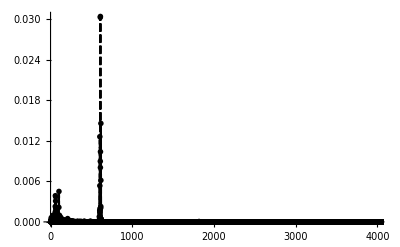

```mathematica
(* apply filter if needed *)
newFiltered =BandpassFilter[new, {400, 1000}]
PerDataFiltered = PeriodogramArray[newFiltered];
ListLinePlot[PerDataFiltered,PlotRange->{{0, 4000}, All}]
```